# de Broglie-Bohm pilot-wave description of double-slit experiment

Linearity of quantum dynamics implies consequences that contract our classical notions of nature.

Mohammad Bahrami, Jun. 24,  2018

Quantum theory, as the most successful theory invented so far, defies our classical picture of the world. At the heart of quantum mysteries is the interference experiments (e.g., the double-slit experiment as the archetype). The observation of interference pattern is usually interpreted as the wave nature of quantum systems; while its disappearance is usually considered as the fingerprint of particle features. The standard quantum theory does not prov

## Experimental parameters and physical constants

physical constants

```mathematica
c=QuantityMagnitude@UnitConvert[Quantity["SpeedOfLight"]];
eV=QuantityMagnitude@UnitConvert[Quantity["Electronvolts"]];
h=QuantityMagnitude@UnitConvert[Quantity["PlanckConstant"]];
ℏ=QuantityMagnitude@UnitConvert[Quantity["ReducedPlanckConstant"]];
amu=QuantityMagnitude@UnitConvert[Quantity["AtomicMassUnit"]];
nano=10^-9;
```

Gaussian wavepacket

```mathematica
ψ[x0_,x_,t_]:=Exp[ -(x-x0 )^2/(4 σ^2(1+(ⅈ ℏ t)/(2m σ^2)))];
```

location of center of Gaussians for n-slits (center of n-slits)

```mathematica
slitPosition[d_,n_Integer]:=d Range[0,n-1]-If[OddQ[n],(n-1)/2 d,(n/2-1)d+d/2];
```

superposition of Gaussians from n-slits

```mathematica
(*ϕ[d_,n_,x_,t_]:=1/(√n)Total@(ψ[#,x,t]&/@slitPosition[d,n]);*)
ϕ[d_,n_,x_,t_]:=1/(√n)If[EvenQ[n],Sum[ψ[-(d/2+(i-1)d),x,t]+ψ[d/2+(i-1)d,x,t],{i,n/2}],ψ[0,x,t]+Sum[ψ[i d,x,t]+ψ[- i d,x,t],{i,(n-1)/2}]];
```

ticks for the x-axis along the slits

```mathematica
ticks[d_,n_]:={{None,None},{MapThread[{#1,#2}&,{slitPosition[d,n],slitPosition["d",n]}],None}};
```

plotting the pattern

```mathematica
Manipulate[
finalTime=100(m σ^2)/ℏ;
σ=a/4;
(*n=1;d=100*10^-9;a=50*10^-9;*)
xmax=500nano;xmin=-xmax;
m=500amu;
Quiet@DensityPlot[Abs[ϕ[d,n,x,t]]^2,{x,xmin,xmax},{t,0,finalTime},PlotPoints->50,FrameTicks->ticks[d,11],Mesh->None,ColorFunction->"SunsetColors",AspectRatio->1],Row[{Control[{{n,1},1,10,1}], "  # slits = ",Dynamic[n]}],Row[{Control[{{d,100*nano},100*nano,1000*nano}], "  gap between slits = ",Dynamic[d/nano], " nm"}],Row[{Control[{{a,50*nano},50*nano,Round[d/nano]nano}], "  width of slits = ",Dynamic[a/nano], " nm"}]]
```

## de Broglie-Bohm quantum trajectories

Add more sections as needed to explain the topic....

```mathematica
bohmTrajectory[n_,q0_,tf_]:=Module[{guidingDE,nde},
guidingDE=q'[t]==ℏ/m Im[Conjugate[ϕ[d,n,q[t],t]] D[ϕ[d,n,q[t],t],q[t]]]/(ϕ[d,n,q[t],t]Conjugate[ϕ[d,n,q[t],t]]);
nde=NDSolve[{guidingDE,q[0]==q0},q,{t,0,tf}];
ParametricPlot[{Evaluate[q[t]/.nde],t},{t,0,tf}]]
initialPositions[d_,n_]:=Table[#+i,{i,-a/4,a/4,a/8}]&/@slitPosition[d,n]//Flatten;
n=6;d=100nano;a=50nano;
Show[bohmTrajectory[n,#,.5finalTime]&/@initialPositions[d,n],PlotRange->All]
Clear[n,d,a]
```

-Graphics-

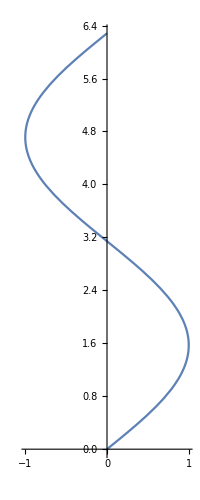



```mathematica
ParametricPlot[{Sin[x],x},{x,0,2π}]
Plot[{Sin[x]},{x,0,2π}]
```

```mathematica
conjψ[x0_,x_,t_]:=Exp[ -(x-x0 )^2/(4 σ^2(1-(ⅈ ℏ t)/(2m σ^2)))];
conjϕ[d_,n_,x_,t_]:=1/(√n)If[EvenQ[n],Sum[conjψ[-(d/2+(i-1)d),x,t]+conjψ[d/2+(i-1)d,x,t],{i,n/2}],conjψ[0,x,t]+Sum[conjψ[i d,x,t]+conjψ[- i d,x,t],{i,(n-1)/2}]];
ρ[d_,n_,x_,t_]:=(ϕ[d,n,x,t])conjϕ[d,n,x,t];
```

```mathematica
qQ[d_,n_,x_,t_]:=(-ℏ^2/(4m))/(10^-13 eV)((Derivative[0,0,2,0][ρ][d,n,x,t])/ρ[d,n,x,t]-1/2((Derivative[0,0,1,0][ρ][d,n,x,t])/ρ[d,n,x,t])^2);
```

```mathematica
n=2;d=100nano;a=50nano;
finalTime=100(m σ^2)/ℏ;
σ=a/4;xmax=500nano;xmin=-xmax;
m=500amu;
qQ[d,2n,0,finalTime]
DiscretePlot3D[qQ[d,n,q,t],{q,xmin,xmax,xmax/100},{t,0,finalTime,.01finalTime}]
```

7.3316+0. ⅈ

General::munfl: (9.57585×10^-175+0. ⅈ) (4.89671×10^-156+0. ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (3.06427×10^-165+0. ⅈ) (3.06427×10^-165+0. ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

## Further explorations

A. Zeilinger, R. Gahler, C.G. Shull, W. Treimer, and W. Mampe, Rev. Mod. Phys. 60, 1067 (1988).

## Author contact information

mbahram@calstatela.edu

(We recommend using your wolfram ID, but any address where you would like to be contacted about this publication should work.)

## Guidelines for the Author

### Image

Try to use images created in the Wolfram Language as much as possible

If an external image is the only way to go, use Import to get the image into the notebook and reverse close the In/Out cell-group  to hide the input cell.

### Text

Use minimal text in small pieces to explain the topic and transition between pieces of code. One or two lines of text at a time should suffice.

Sub-guideline two

### CodeText

Before each line of code, add a single line in CodeText style, as a lead-in, to say what the code that follows will do.

End this line with a colon

Make a map of Monaco:

```mathematica
GeoGraphics[Entity["Country","Monaco"]]
```

-Graphics-

### Code

Keep code simple and straightforward; code cell should be at most 3 lines long

Breakup complicated lengthy code into multiple segments and separate with CodeText lead-ins explaining each segment

Try to create simple visualizations whenever possible to illustrate the topic and add visual interest

Extra code (for example, visualization options to simply make the output look pretty) can be distracting and take away focus from the main functionality. Either avoid these or use Iconize to hide them.

Instead of

```mathematica
Plot[Sin[x], {x, 1, 10}, PlotStyle -> {Red, Dashed, Thick}]
```

Use

```mathematica
Plot[Sin[x],{x,1,10},]
```

If using a Manipulate, remember to set SaveDefinitions->True, if it refers to definitions not contained within it. This will allow the Manipulate to work without having to re-evaluate the notebook, for every new session.

Include Data Repository

Include Function Repository (mention coming soon)

DensityPlot::plln: Limiting value -500 nano in {Charting`Private`pvar$8010,-500 nano,500 nano} is not a machine-sized real number.

DensityPlot::plln: Limiting value -500 nano in {Charting`Private`pvar$8031,-500 nano,500 nano} is not a machine-sized real number.

General::stop: Further output of DensityPlot::plln will be suppressed during this calculation.